## Яковчик И.А.

## Lab_work_2: Символьные вычисления в системе Mathematica

## 2.1

### 1. Придумайте и определите символьное выражение содержащее не менее трех слагаемых, причём хотя бы одно из них должно быть рациональным выражением

```mathematica
fun1 = (4*(x^2+10)*(x-y))/((2 x^2-8)*(x-y)) +(x+y)^3+x^2+y^2;
Expand[fun1](*Раскрываем скобки и представляем в виде суммы*)
```

x^2+x^3+40/(-8+2 x^2)+(4 x^2)/(-8+2 x^2)+3 x^2 y+y^2+3 x y^2+y^3

```mathematica
ExpandAll[fun1]
```

x^2+x^3+40/(-8+2 x^2)+(4 x^2)/(-8+2 x^2)+3 x^2 y+y^2+3 x y^2+y^3

```mathematica
Factor[fun1](*Выносим за скобки общий множитель и представляем в виде произведения*)
```

(20-2 x^2-4 x^3+x^4+x^5-12 x^2 y+3 x^4 y-4 y^2-12 x y^2+x^2 y^2+3 x^3 y^2-4 y^3+x^2 y^3)/((-2+x) (2+x))

```mathematica
Together[fun1](*Собираем из простых частей сумму*)
```

(20-2 x^2-4 x^3+x^4+x^5-12 x^2 y+3 x^4 y-4 y^2-12 x y^2+x^2 y^2+3 x^3 y^2-4 y^3+x^2 y^3)/(-4+x^2)

```mathematica
Apart[fun1](*Раскладываем на простые дроби*)
```

(20-2 x^2-4 x^3+x^4+x^5)/((-2+x) (2+x))+3 x^2 y+(1+3 x) y^2+y^3

```mathematica
Cancel[fun1](*Сокращаем числители и заменатели*)
```

x^2+(2 (10+x^2))/(-4+x^2)+y^2+(x+y)^3

```mathematica
Simplify[fun1](*И наконец, сокращаем наше выражение*)
```

x^2+(2 (10+x^2))/(-4+x^2)+y^2+(x+y)^3

### 2. Приведите своё выражение к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения обозначив его другим именем. С помощью функции Collect представьте это выражение в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных, например х и коэффициент х^n. Используйте функции Exponent и Coefficient

```mathematica
fun2 = Numerator[Together[fun1]];(*Сначала приводим выражение к общему знаменателю*)
```

```mathematica
20-4 x^2-2 x^3+x^4+x^5-12 x^2 y+3 x^4 y-4 y^2-12 x y^2+x^2 y^2+3 x^3 y^2-4 y^3+x^2 y^3
```

```mathematica
Collect[fun2,x](*Затем представляем в виде полинома по степеням х*)
```

```mathematica
20+x^5-4 y^2-12 x y^2-4 y^3+x^4 (1+3 y)+x^3 (-2+3 y^2)+x^2 (-4-12 y+y^2+y^3)
```

```mathematica
Exponent[fun2,x](*Вычисляем максимальную степень переменной х*)
```

5

```mathematica
Coefficient[fun2,x,Exponent[fun2,x]](*Получаем коэффициент многочлена с наибольшей степенью переменной х*)
```

1

```mathematica
Coefficient[fun2,x,2](*Коэфициент многочлена при переменной х^2*)
```

-4-12 y+y^2+y^3

```mathematica
CoefficientList[fun2,x](*Список коэффициентов переменной х*)
```

{20-4 y^2-4 y^3,-12 y^2,-4-12 y+y^2+y^3,-2+3 y^2,1+3 y,1}

## 2.2

### 1. С помощью функции D вычислите производную функции x^ncos(x)

```mathematica
D[x^n*Cos[x], x](*Получил производную функции*)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2. Вычислите следующие производные: d/dx (ax^3+2 x^2); d^3/dx^3(4 x^2-5x+8-3/x); d^5/(dx^3*dy^2) (x^3*y^2+3 x^2)

```mathematica
D[a*x^3+2 x^2,x](*Получил результаты неколькольких производных*)
```

4 x+3 a x^2

```mathematica
D[4 x^2-5x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[x^3*y^2+3 x^2,{x,3},{y,2}]
```

12

### 3. Используя функцию Integrate вычислите интеграл: ∫dx/(x^2-1)

```mathematica
Integrate[1/(x^2-1),x](*Получение проинтегрированной функции, одна произвольнная интегрирования / нашли первоборазную, т.к не т С*)
```

1/2 Log[1-x]-1/2 Log[1+x]

### 4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают подынтегральными выражениями: ∫x^3/(x^2+1)dx; ∫1/(x^3+1)dx

```mathematica
(*Вычислиние интегралов, а затем с помощью производной убедился в совпадении подынтегральных выражений*)
```

```mathematica
Integrate[x^3/(x^2+1),x](*Вычислиние интеграла*)
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Simplify[D[x^2/2-1/2*Log[1+x^2],x]](*Вычислиние производной, для подтверждения совпадений с подынтыгральными выражениями, данными в условии*)
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x](*Вычислиние интеграла*)
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]](*Вычислиние производной, для подтверждения совпадений с подынтыгральными выражениями,данными в условии*)
```

1/(1+x^3)

### 5. Вычислите определённый интеграл: ∫_1^4 (5x-2 √x+32/x^3)dx

```mathematica
Integrate[5x-2 √x+32/x^3,{x,1,4}](*Функция, вычисляющая определённый интеграл*)
```

259/6

### 6. Вычислите интегралы: ∫_0^1 (1+x^4)^(1/3)dx; ∫_0^1. (1+x^4)^(1/3)dx(Обратить внимание на действительное число “1.” Сравнить полученные результаты).

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}]
```

```mathematica
Hypergeometric2F1[-1/3,1/4,5/4,-1](*Гипергеометрическая функция*)
```

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}](*Только при наличии действительного числа, происходит автоматическое вычисление, получаем гиперметриотрическую функцию, число являестя действительым, точность получаем до 6 значений*)
```

1.05753

## 2.3

### 1. Используя функцию Solve,решить уравнение: ax^4+x^2+3=0

```mathematica
Solve[a x^4+x^2+3==0,x](*Решение линейного уравнения *)
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

### 2. Найти точное решение системы уравнений: {x^2+y=1 y^2-x^2=2

```mathematica
Solve[x^2+y==1&&y^2-x^2==2,{x,y},Reals](*Решение системы уравнений*)
```

{{x→-√(1/2 (3+√13)),y→1+1/2 (-3-√13)},{x→√(1/2 (3+√13)),y→1+1/2 (-3-√13)}}

### 3. Решить систему уравнений, найти комплексные значения: {x^2-y^2=1 y^3+x=5

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5,{x,y}](*Решение системы уравнений*)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

### 4. Найти общие решения дифференциальных уравнений, используя функцию DSolve: y’(x)-y(x)tg(x)=x; y’(x)+y(x)tg(x)=1/cos(x)

```mathematica
DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x](*Общее решение 1-го дифф уравнения*)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[y'[x]+y[x]*Tan[x]==1/Cos[x],y[x],x](*Общее решение 2-го дифф уравнения*)
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

```mathematica
func1=DSolve[{y'[x]-y[x]*Tan[x]==x,y[0]==1},y[x],{x,-5,5}](*-5 и 5 - граничные условия для 1-го дифф уравнения*)
```

{{y[x]→1+x Tan[x]}}

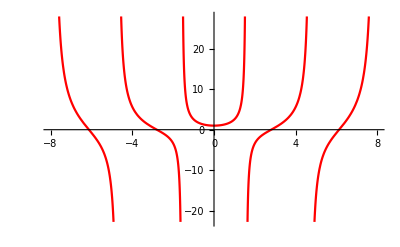

```mathematica
Plot[Evaluate[y[x]/.func1],{x,-8,8},PlotStyle->Red](*Построение графика для 1-го дифф уравнения*)
```

```mathematica
func2=DSolve[{y'[x]+y[x]*Tan[x]==1/Cos[x],y[0]==1},y[x],{x,-5,5}](*-5 и 5 - граничные условия для 2-го дифф уравнения*)
```

{{y[x]→Cos[x]+Sin[x]}}

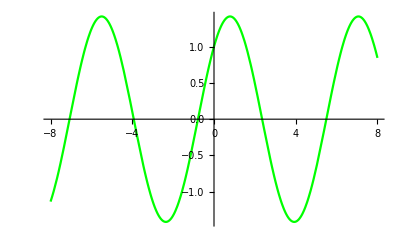

```mathematica
Plot[Evaluate[y[x]/.func2],{x,-8,8},PlotStyle->Green](*Построение графика для 2-го дифф уравнения*)
```

### 5.Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде: y’’(x)-y’(x)+x*y(x)=0

```mathematica
f=DSolve[y''[x]-y'[x]+x*y[x]==0,y[x],x]
```

```mathematica
{{y[x]->ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}(*общее решение.*)
```

```mathematica
f1=FullSimplify[DSolve[{y''[x]-y'[x]+x*y[x]==0,y'[0]==0,y[0]==1},y[x],x]](*Задал граничные условия и нашёл решение в символьном виде*)
```

{{y[x]→1/2 ⅇ^(x/2) π ((AiryAi[1/4]-2 AiryAiPrime[1/4]) AiryBi[1/4-x]-AiryAi[1/4-x] (AiryBi[1/4]-2 AiryBiPrime[1/4]))}}

```mathematica
f2=NDSolve[{y''[x]-y'[x]+x*y[x]==0,y'[0]==0,y[0]==1},y[x],{x,-5,13}](*Нашёл численное решение*)
```

```mathematica
{{y[x]->InterpolatingFunction[…][x]}}
```

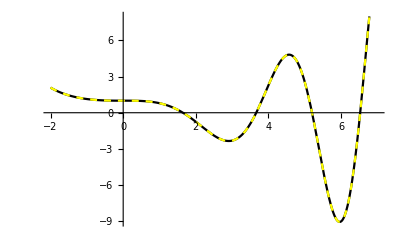

```mathematica
graphic=Show[Plot[Evaluate[y[x]/.f1],{x,-2,7},PlotStyle->Black],Plot[Evaluate[y[x]/.f2],{x,-2,7},PlotStyle->{Dashed,Yellow}]]
(*На одной коорд плоскости отобразил численное и символьное решение данного ур-я. Из графиков ниже видно, что эти решения совпадают*)
```